```mathematica
Integrate[(ρ/(r^2+2ρ r Cos[ψ[t]]+ρ^2)^(3/2)),ρ]
```

((-6870000-ρ Cos[ψ[t]]) Csc[ψ[t]]^2)/(6870000 √(47196900000000+ρ^2+13740000 ρ Cos[ψ[t]]))

```mathematica
Mz=Simplify[ μ λ r Sin[ψ[t]](((-r-(L[t]/2) Cos[ψ[t]]) Csc[ψ[t]]^2)/(r √(r^2+(L[t]/2)^2+2 r (L[t]/2) Cos[ψ[t]]))-((-r+(L[t]/2) Cos[ψ[t]]) Csc[ψ[t]]^2)/(r √(r^2+(L[t]/2)^2-2 r (L[t]/2) Cos[ψ[t]])))]
```

-(30000000000000000 (-13740000+(100+t) Cos[ψ[t]]) Csc[ψ[t]])/(√(188787600010000+200 t+t^2-27480000 (100+t) Cos[ψ[t]]))-(30000000000000000 (13740000+(100+t) Cos[ψ[t]]) Csc[ψ[t]])/(√(188787600010000+200 t+t^2+27480000 (100+t) Cos[ψ[t]]))

```mathematica
eqn = I3'[t]ψ'[t]+I3[t]ψ''[t]==Mz
```

25 (100+t)^2 ψ'[t]+25/3 (100+t)^3 ψ''[t]==-(30000000000000000 (-13740000+(100+t) Cos[ψ[t]]) Csc[ψ[t]])/(√(188787600010000+200 t+t^2-27480000 (100+t) Cos[ψ[t]]))-(30000000000000000 (13740000+(100+t) Cos[ψ[t]]) Csc[ψ[t]])/(√(188787600010000+200 t+t^2+27480000 (100+t) Cos[ψ[t]]))

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3.11876×10^-11.

InterpolatingFunction::dmval: Input value {2.04082} lies outside the range of data in the interpolating function. Extrapolation will be used.

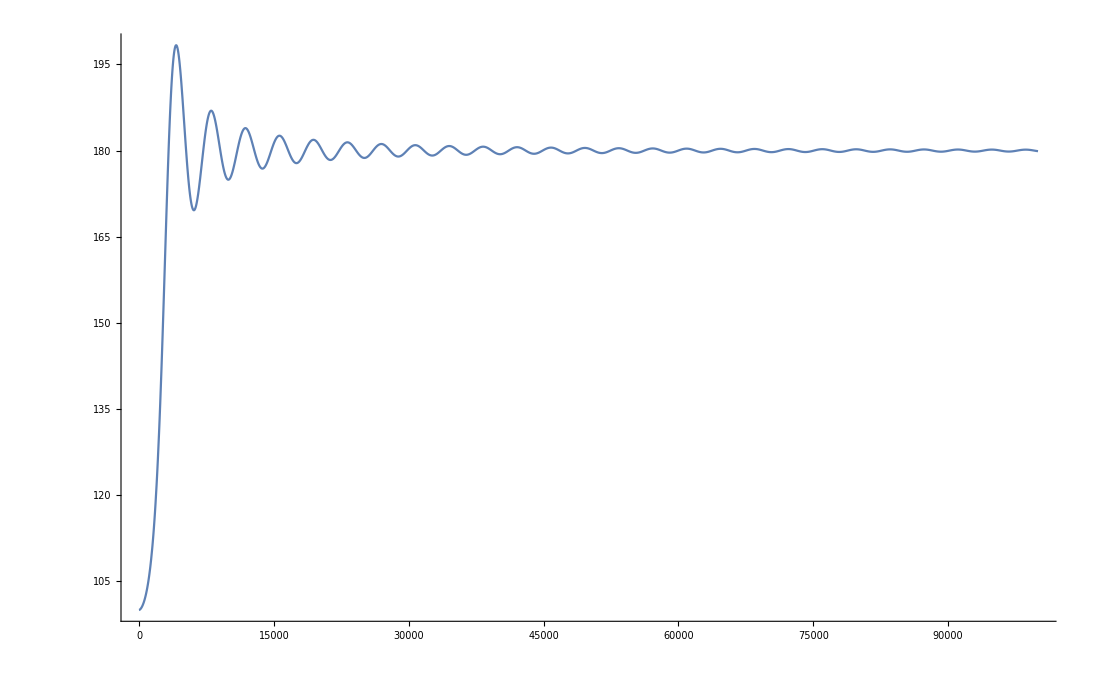

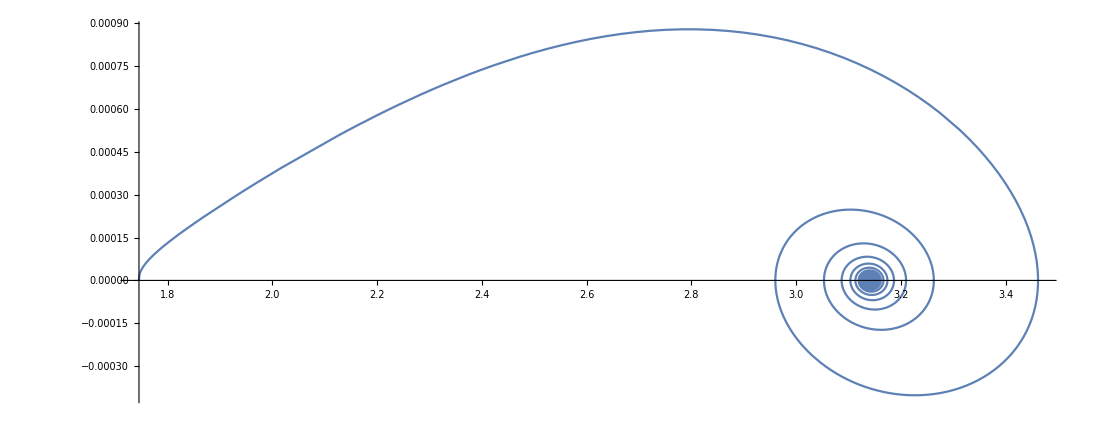

```mathematica
μ=3*10^14;
λ = 100;
r = 6870000;
L[t_]:= 100 +t;
I3[t_]:= 1/12 λ L[t]^3;
range = 100000;
Manipulate[
system = NDSolve[{eqn,ψ[0]==z °,ψ'[0]==0},ψ,{t,0,range}];
psi = ψ /. system[[1]];
psid = ψ' /. system[[1]];
ParametricPlot[{psi[t],psid[t]},{t,0,range},PlotRange->All,AspectRatio->Full],{z,-360,360,1}]
```